## Perturbation methods on coupled differential equation

### Numerical Solution

```mathematica
eq3:={y''[t]==y'[t]  0.001 √((x'[t])^2+(y'[t])^2),x''[t]==-1-0.001x'[t]  √((x'[t])^2+(y'[t])^2),x[0]==0,y[0]==0,x'[0]==1,y'[0]==1}
NDSolve[eq3,{x[t],y[t]},{t,0,2}]
```

{{x[t]→InterpolatingFunction[…][t],y[t]→InterpolatingFunction[…][t]}}

```mathematica
{xans[t_],yans[t_]}={x[t],y[t]}/.Flatten[NDSolve[eq3,{x[t],y[t]},{t,0,2}]]
```

{InterpolatingFunction[…][t],InterpolatingFunction[…][t]}

```mathematica
graphx=Plot[xans[t],{t,0,10},AxesLabel->{"t","y"},PlotLabel->"Numerical Solution of x"];
```

```mathematica
graphy=Plot[yans[t],{t,0,10},AxesLabel->{"t","y"},PlotLabel->"Numerical Solution of y"];
```

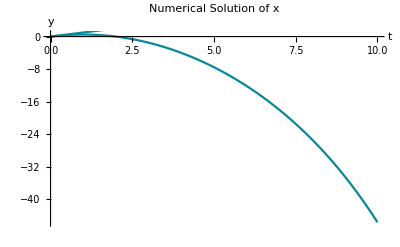

```mathematica
Show[graphx,graphy]
```

### Analytic Solution

```mathematica
xhand[t_]:=-t^2/2+t+0.001  (t^2/4-t^3/3+t^4/12)
yhand[t_]:=t+0.001  ((3  t^2)/4-t^3/6+t^4/24)
```

```mathematica
graphxh=Plot[xhand[t],{t,0,10},AxesLabel->{"t","y"},PlotLabel->"Numerical Solution of Equation 1"];
graphyh=Plot[yhand[t],{t,0,10},AxesLabel->{"t","y"},PlotLabel->"Numerical Solution of Equation 1"];
```

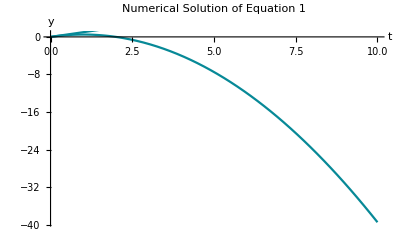

```mathematica
Show[graphxh,graphyh]
```

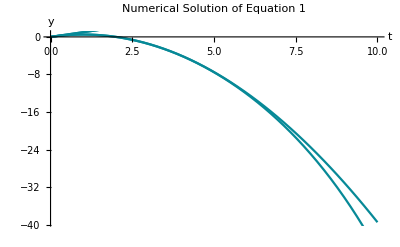

```mathematica
Show[graphxh, graphyh,graphx,graphy]
```